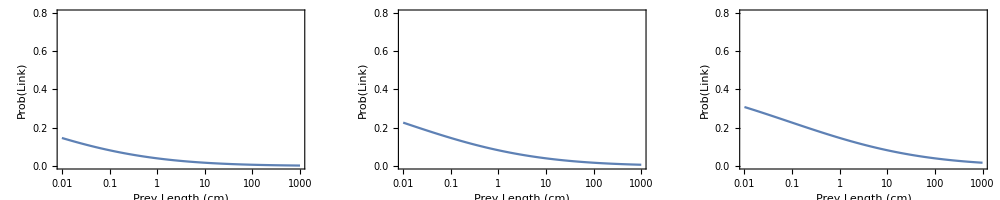

```mathematica
p = Exp[alpha + beta*Log[PredMass/PreyMass] + gamma*Log[PredMass/PreyMass]^2];
prob = p/(1+p);
GraphicsGrid[{Table[LogLinearPlot[prob/.{PredMass->i,alpha->-4.07,beta->0.41,gamma->-0.011},{PreyMass,0.01,1000},PlotRange->{0,0.8},Frame->True,FrameLabel->{"Prey Length (cm)","Prob(Link)",ToString[{"Pred Length=",i}]},AspectRatio->0.5,ImageSize->500],{i,{10,100,1000}}]},ImageSize->1000]
```